{0,0,10,12,30,24,20,18,19,15,0,0,0,2}

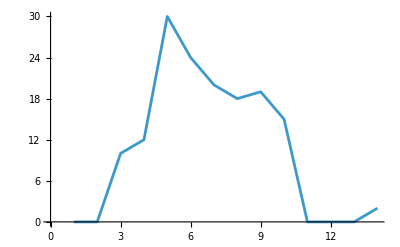

```mathematica
l1={0,0,10,12,30,24,20,18,19,15,0,0,0,2}
ListLinePlot[l1]
```

```mathematica
cwt12=ContinuousWaveletTransform[l1,MexicanHatWavelet[1],{2,4}]
```

ContinuousWaveletData[…]

```mathematica
cwt14=ContinuousWaveletTransform[l1,MexicanHatWavelet[1],{4,4}]
```

ContinuousWaveletData[…]

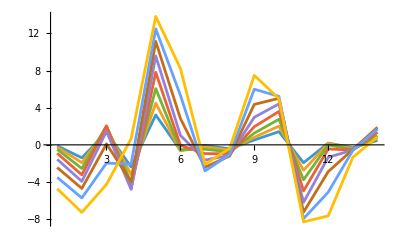

```mathematica
ListLinePlot[cwt12[All,"Values"]//Re,PlotRange->Full]
```

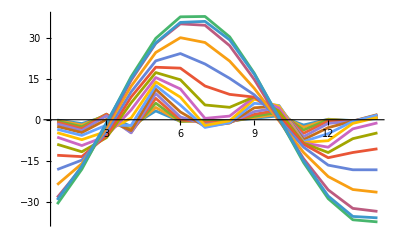

```mathematica
ListLinePlot[cwt14[All,"Values"]//Re,PlotRange->Full]
```

```mathematica
cwt12[All,"Values"][[8]]
```

{-4.72526-3.70159×10^-16 ⅈ,-7.26974-1.37372×10^-16 ⅈ,-4.26282-2.43198×10^-16 ⅈ,0.660352-1.96943×10^-16 ⅈ,13.8243+2.36327×10^-16 ⅈ,8.23601-6.83386×10^-17 ⅈ,-2.09672+2.59215×10^-16 ⅈ,-0.37624+2.97255×10^-16 ⅈ,7.47942+6.08131×10^-17 ⅈ,4.97986+2.97255×10^-16 ⅈ,-8.29551+1.26222×10^-16 ⅈ,-7.65297-6.83386×10^-17 ⅈ,-1.33551+4.20477×10^-18 ⅈ,0.834854-1.96943×10^-16 ⅈ}

```mathematica
cwt14[All,"Values"][[8]]
```

{-4.72526-3.70159×10^-16 ⅈ,-7.26974-1.37372×10^-16 ⅈ,-4.26282-2.43198×10^-16 ⅈ,0.660352-1.96943×10^-16 ⅈ,13.8243+2.36327×10^-16 ⅈ,8.23601-6.83386×10^-17 ⅈ,-2.09672+2.59215×10^-16 ⅈ,-0.37624+2.97255×10^-16 ⅈ,7.47942+6.08131×10^-17 ⅈ,4.97986+2.97255×10^-16 ⅈ,-8.29551+1.26222×10^-16 ⅈ,-7.65297-6.83386×10^-17 ⅈ,-1.33551+4.20477×10^-18 ⅈ,0.834854-1.96943×10^-16 ⅈ}

{0,0,10,12,30,40,60,100,110,111}

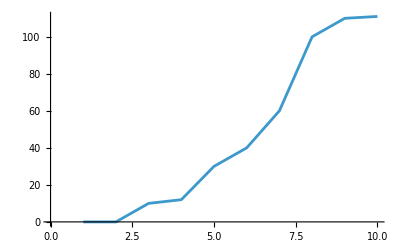

```mathematica
l2={0,0,10,12,30,40,60,100,110,111}
ListLinePlot[l2]
```

```mathematica
cwt2=ContinuousWaveletTransform[l2,MexicanHatWavelet[1],{3,4}]
```

ContinuousWaveletData[…]

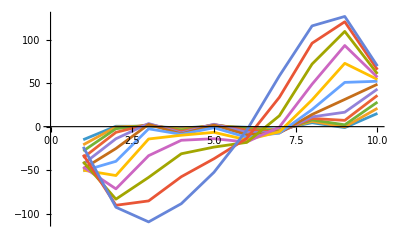

```mathematica
ListLinePlot[cwt2[All,"Values"]]
```

{0.711368,0.54267,0.830005,0.615091,0.745987,0.963387,0.0164338,0.781957,0.153622,0.233933}

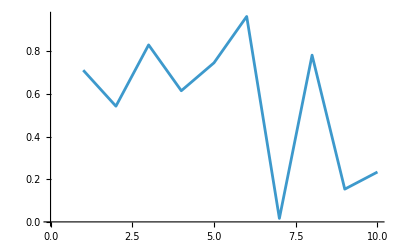

```mathematica
lr=Table[RandomReal[],{10}]
ListLinePlot[lr]
```

```mathematica
cwtr=ContinuousWaveletTransform[lr,MexicanHatWavelet[1]]
```

ContinuousWaveletData[…]

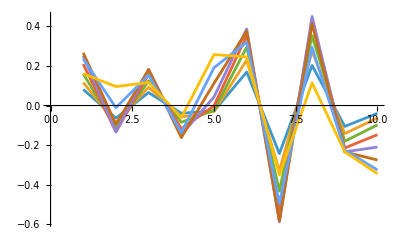

```mathematica
ListLinePlot[cwtr[All,"Values"]]
```

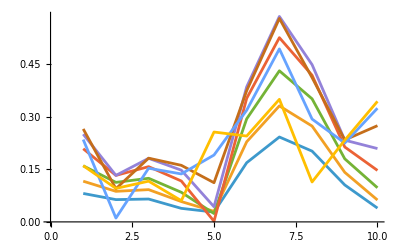

```mathematica
Map[Abs,cwtr[All,"Values"]]//ListLinePlot
```

```mathematica
Map[Norm,cwtr[All,"Values"],{-1}]//ListLinePlot
```

-Graphics-

```mathematica
Map[Re,cwtr[All,"Values"],{-1}]//ListLinePlot
```

-Graphics-

ピーク推定

モジュール読み込み：

```mathematica
Get["/Users/kouamano/gitsrc/SCRIPT_Mathematica/SCRIPTS/Wavelet.txt"]
```

```mathematica
cwt12[All,"Values"]//WTPE
```

2

```mathematica
cwtr[All,"Values"]
```

{{0.0812761,-0.0636708,0.0653454,-0.0386913,-0.0280767,0.169129,-0.24259,0.202228,-0.105568,-0.0393821},{0.11627,-0.0873338,0.0922003,-0.0580982,-0.0301821,0.228985,-0.331504,0.273843,-0.14166,-0.0625213},{0.160304+5.73446×10^-18 ⅈ,-0.11295-5.73446×10^-18 ⅈ,0.124616+5.73446×10^-18 ⅈ,-0.0846211-5.73446×10^-18 ⅈ,-0.0239288+5.73446×10^-18 ⅈ,0.294494-5.73446×10^-18 ⅈ,-0.431761+5.73446×10^-18 ⅈ,0.35167-5.73446×10^-18 ⅈ,-0.180266+5.73446×10^-18 ⅈ,-0.0975578-5.73446×10^-18 ⅈ},{0.209026+6.13245×10^-18 ⅈ,-0.132908-6.13245×10^-18 ⅈ,0.157879+6.13245×10^-18 ⅈ,-0.11689-6.13245×10^-18 ⅈ,-0.00181652+6.13245×10^-18 ⅈ,0.353161-6.13245×10^-18 ⅈ,-0.526461+6.13245×10^-18 ⅈ,0.419137-6.13245×10^-18 ⅈ,-0.214025+6.13245×10^-18 ⅈ,-0.147103-6.13245×10^-18 ⅈ},{0.250679,-0.132882,0.181666,-0.147818,0.0433379,0.38594,-0.587076,0.449299,-0.23357,-0.209576},{0.265658,-0.0948397,0.18209,-0.161674,0.111996,0.374967,-0.581405,0.412302,-0.234145,-0.274949},{0.235279+2.28808×10^-18 ⅈ,-0.0109837-2.28808×10^-18 ⅈ,0.153374+2.28808×10^-18 ⅈ,-0.137081-2.28808×10^-18 ⅈ,0.191018+2.28808×10^-18 ⅈ,0.319135-2.28808×10^-18 ⅈ,-0.494336+2.28808×10^-18 ⅈ,0.293864-2.28808×10^-18 ⅈ,-0.225401+2.28808×10^-18 ⅈ,-0.324869-2.28808×10^-18 ⅈ},{0.160636,0.0956759,0.116373,-0.0606752,0.256818,0.245319,-0.350237,0.114086,-0.233532,-0.344463}}

```mathematica
WTPE[cwtr[All,"Values"]]
```

3

```mathematica
WTPE[cwtr[All,"Values"],"position"]
```

{{3},{6},{8}}